```mathematica
<<KPlots`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Mathematica Based Video Analysis

```mathematica
raw = Import["comparing_with_Simons_routine_2014-11-06.csv"];
```

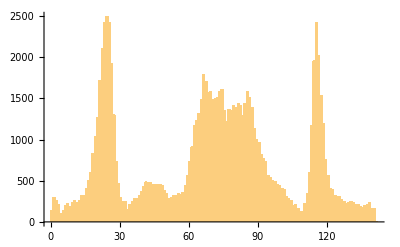

```mathematica
Histogram[ raw⟦All, 2⟧ , {1}]
```

#### Simons routine

```mathematica
other = Import["Simon_and_Yizhou_routine_2014-11-06.xlsx"]⟦1,2;;⟧;
yizhou = other⟦;;, {1,2}⟧;
simon = other⟦;;, {4,5}⟧;
simon =Transpose@{simon⟦;;,1⟧-51, simon⟦;;,2⟧};
```

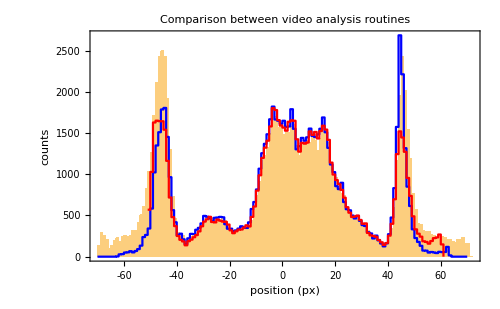

( | )

```mathematica
Show[

Histogram[ raw⟦All, 2⟧ -70, {1}],

ListPlot[yizhou, Joined->True, InterpolationOrder->0, PlotStyle->Blue],

ListPlot[simon, Joined->True, InterpolationOrder->0, PlotStyle->Red],

PlotLabel->"Comparison between video analysis routines",
FrameLabel-> {"position (px)","counts"},
ImageSize-> 500,
KPlotsTheme
]
{{LineLegend[{Red,Blue},{"Simon's routine","Yizhou's routine"}],
SwatchLegend[{Lighter@Orange},{"Karolis' routine"}]}}
```